# 09.26.2023 How to Differentiate and Integrate in Mathematica? Salizhan Kylychbekov

```mathematica
f[x_]:=(x-1)^2/(x^2+1)
D[f[x],x]
```

-(2 (-1+x)^2 x)/((1+x^2)^2)+(2 (-1+x))/(1+x^2)

```mathematica
f'[x]
```

-(2 (-1+x)^2 x)/((1+x^2)^2)+(2 (-1+x))/(1+x^2)

```mathematica
Simplify[%114]
```

(2 (-1+x^2))/((1+x^2)^2)

```mathematica
f''[x]
```

(8 (-1+x)^2 x^2)/((1+x^2)^3)-(2 (-1+x)^2)/((1+x^2)^2)-(8 (-1+x) x)/((1+x^2)^2)+2/(1+x^2)

```mathematica
FullSimplify[(8 (-1+x)^2 x^2)/((1+x^2)^3)-(2 (-1+x)^2)/((1+x^2)^2)-(8 (-1+x) x)/((1+x^2)^2)+2/(1+x^2)]
```

-(4 x (-3+x^2))/((1+x^2)^3)

```mathematica
f'[0.5]
```

-0.96

```mathematica
f''[0.5]
```

2.816

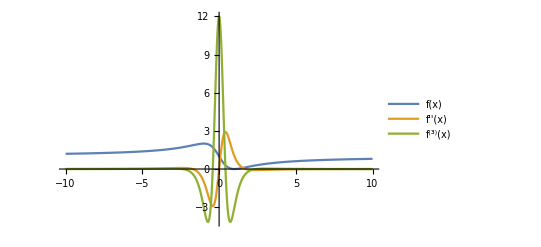

```mathematica
Plot[{f[x],f''[x],f'''[x]},{x,-10,10}, PlotLegends->"Expressions", PlotRange->All]
```

## Integration

```mathematica
g[x]:=x^2+x^3
```

```mathematica
Integrate[g[x],x]
```

x^3/3+x^4/4

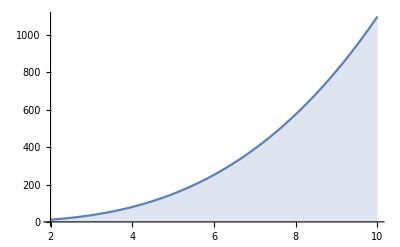

```mathematica
Plot[g[x], {x, 2,10}, Filling->Axis]
```

```mathematica
t[x]:=x^2+x^3+E^x
```

```mathematica
Integrate[t[x], x]
```

ⅇ^x+x^3/3+x^4/4

```mathematica
Integrate[g[x],{x,2,10}]
```

8480/3

```mathematica
∫_0^2 xⅆx
```

2

```mathematica
NIntegrate[1/Sqrt[x+y^2+z^3],{x,0,1},{y,0,2},{z,0,3}]
```

3.08557